# Quantum Enhanced Support Vector Machine

In this notebook, we will explore a quantum algorithm developed to enhance a machine learning (ML) algorithm. In particular, we will study the quantum enhanced support vector machine, introduced by the scientific staff of IBM in [1].

-Graphics-                    -Graphics-

We will now focus on a specific supervised learning algorithm, the support vector machine. But let us first introduce the dataset we want to classify.

### Python Configuration

Install Wolfram quantum framework:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
<<Wolfram`QuantumFramework`
<<Wolfram`QuantumFramework`QuantumOptimization`
```

PacletObject[…]

Set up Classiq:

```mathematica
classiq=ClassiqSetup[{"Session","ClassiqVersion"},"CheckDependencies"->{"pyomo","scikit-learn"},"InstallPackages"->{"scikit-learn"}]
```

Installing latest Classiq version

```mathematica
session=classiq["Session"]
```

ExternalSessionObject[…]

## Breast Cancer Dataset

## Classical SVM—Intuition

We want to classify the Breast Cancer Wisconsin (Diagnostic) dataset ). The dataset consists of 569 training examples, with each having 32 attributes such as the perimeter, the texture, the area, etc. The diagnosis of this data can be malignant or benign. 
Here is an image that demonstrates the data:

-Graphics-
Taken from “Islam, T., Sheakh, M.A., Tahosin, M.S. et al., “Predictive Modeling for Breast Cancer Classification in the Context of Bangladeshi Patients by Use of Machine Learning Approach with Explainable AI,” Scientific Reports 14, 8487 (2024). https://doi.org/10.1038/s41598-024-57740-5

### Dimensionality Reduction: Principal Component Analysis

For the sake of simplicity, which will be particularly relevant for the quantum-enhanced version of the algorithm, we do a dimensional reduction of our data from 32 attributes to 2, with the help of a principal component analysis (PCA). Such an unsupervised algorithm finds the principal axes of the data with a singular value decomposition:

import sys
utils_folder = <* NotebookDirectory[] *>
if utils_folder not in sys.path :
   	sys.path.insert(0, utils_folder)

import numpy as np
from utils.dataset import breast_cancer
from sklearn.datasets import make_blobs
from utils.dataset_helper import split_dataset_to_data_and_labels
from sklearn import svm #pip install scikit-learn
from utils.utils import svm_utils
from matplotlib import pyplot as plt
#%matplotlib inline


import time
start_time = time.time()

Generally, multiple feature learning can be used. In many cases, features can exhibit strong correlations. This characteristic enables one to reduce the dimensionality of the data while maintaining inference abilities. Let us first reduce the dimensionality of the data using PCA:

n = 2 # number of principal components kept
training_dataset_size = 15
testing_dataset_size = 11

sample_Total, training_input, test_input, class_labels = breast_cancer(training_dataset_size, testing_dataset_size, n)

data_train, _ = split_dataset_to_data_and_labels(training_input)
data_test, _ = split_dataset_to_data_and_labels(test_input)

print(data_train[0][0:5])

[[ 0.15466634  0.55598151]

[-0.1599017  -0.42952926]

[-0.31057173 -0.19019869]

[-0.13147661 -0.39451755]

[-0.30944272 -0.4377148 ]]

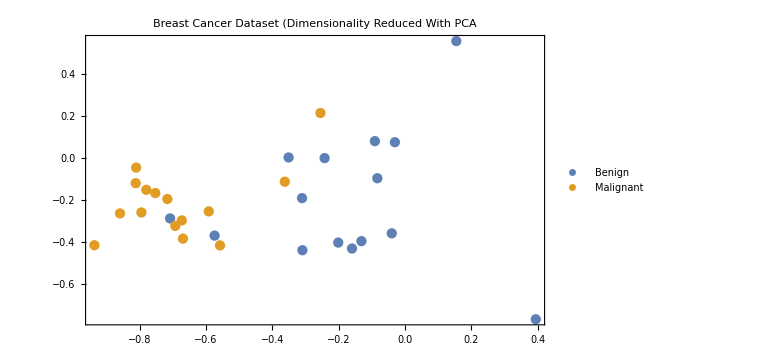

## Linear Support Vector Machine

### Linearly Separable vs. Inseparable Sets

We first emphasize that there are two types of data that can be classified by these algorithms: linearly separable datasets and nonlinearly separable datasets. Our dataset is clearly not linearly separable. We show two examples in the different classes here below:

centers = [(2.5,0),(0,2.5)]
x, y = make_blobs(n_samples=100, centers=centers, n_features=2,random_state=0,cluster_std=0.5)

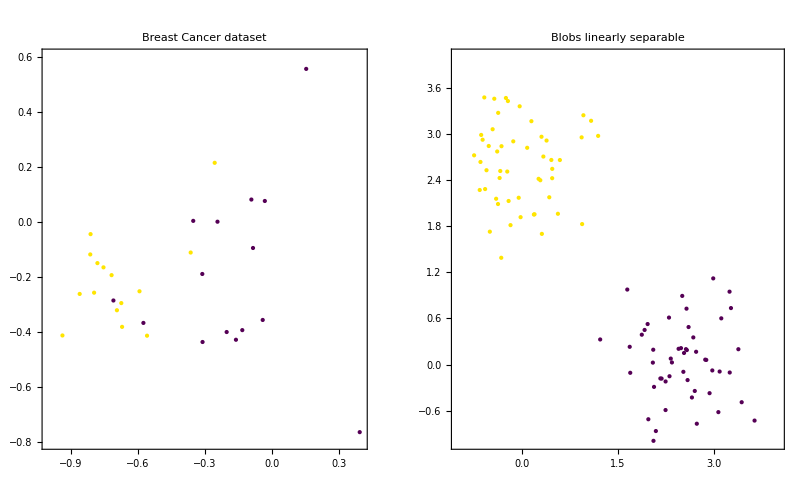

```mathematica
blobsLinear=GatherBy[Thread[Normal[ExternalEvaluate[session,#]&/@{"x","y"}]],Last][[All,All,1]];
GraphicsRow[ListPlot[#[[1]],Frame->True,PlotRange->#1⟦2⟧,Axes->False,AspectRatio->Full,PlotStyle->{{Darker[Purple],PointSize->Medium},{Hue[0.15,1,1],PointSize->Medium}},ImageSize->Large,PlotLabel->#1⟦3⟧]&/@{{dataTrain,{{-1,0.4},{-0.8,0.6}},"Breast Cancer Dataset"},{blobsLinear,{{-1,4},{-1,4}},"Blobs Linearly Separable"}}]
```

We begin by considering a linearly separable dataset. While it is possible to separate the data using a linear decision boundary, there exist infinitely many such linear separators, as illustrated in the figure below. The objective, however, is not merely to find any separating hyperplane, but rather to identify one that achieves good generalization performance on unseen data:

-Graphics-

## Support Vector Machine—Mathematical Background

-Graphics-

Taken from Wikipedia: https://en.wikipedia.org/wiki/Support_vector_machine

The support vector machine algorithm tries to find the parameters  and  such that the training data is linearly separated by a maximum-margin hyperplane. In the current case, our task is for binary classification with labels . Thus, the algorithm aims to satisfy

-Graphics-

The optimization problem therefore consists of maximizing the distance between the two hyperplanes  (or minimizing ) given the constraints , . This problem corresponds to the optimization of a quadratic problem with linear constraints

and has therefore a unique extremum. The latter can be found with a gradient-descent technique.

In some of the problems, one would prefer to have a control on the margins by giving a weight to every point of the dataset, which would be an hyperparameter. This can done by considering the following problem:

For , we recover the hard margin case, i.e. the ideal scenario where the data is perfectly linearly separable and there are no classification errors. The value of C allows one to control the size of the margins.

Combining the inequalities  and , the minimization problem can be rewritten as

.

The second term of this inequality is the so-called Hinge loss, and the SVM problem can be seen as a minimization of the Hinge loss with a  regularization of the weights. Finally, we notice that the problem still has a unique minimum.

One can show that the optimization problem of the SVM is equivalent to the minimization of its dual formulation. For example, in the case of the soft margins, the dual problem takes the form

.

One of the advantages of this formulation is that it only involves the scalar products . This will be a crucial point when we go to kernel methods.

## Support Vector Machine with Kernel

As discussed, data is not always linearly separable in its original feature space. Kernel methods offer an elegant solution by implicitly mapping the data into a higher-dimensional space where a linear classifier can be applied. For instance, a one-dimensional dataset that cannot be separated by a straight line can become separable when transformed using a nonlinear map such as , lifting the data into a two-dimensional space. In the dual formulation of the support vector machine, only scalar products between data points are required. After mapping, these take the form . The key point of the kernel trick is that the scalar product can often be computed directly using a kernel function, without explicitly performing the embedding. A prominent example is the Gaussian (or RBF) kernel, which corresponds to a mapping into an infinite-dimensional space and still allows the scalar product to be computed analytically.

The choice of kernel determines the shape of the decision boundary in the original space. Linear kernels yield straight lines, while nonlinear kernels, such as the Gaussian, allow for complex, flexible boundaries that can adapt to intricate data distributions—enabling accurate classification even in cases where the classes are highly intertwined, as exemplified in the figure below:

```mathematica
Import[NotebookDirectory[]<>"files/pictures/nonlinear_separation.png"]
```

-Graphics-

## Hands-on Session on Support Vector Machine

Before going to the quantum approach, we will implement both the linear and kernel SVM algorithms for the breast cancer dataset. First, let’s have a look at our dataset.

## Classical SVM—Becoming Familiar with the Dataset

### Breast Cancer Dataset Plot

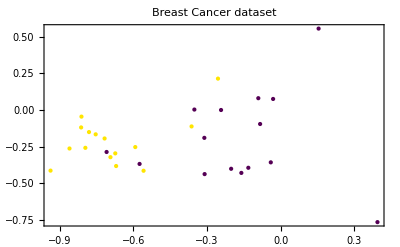

```mathematica
ListPlot[dataTrain,PlotLabel->"Breast Cancer dataset",]
```

### Linear SVM

We then define a linear SVM classifier and train it on the dataset:

model= svm.LinearSVC()
model.fit(data_train[0], data_train[1])

ExternalObject[…]

accuracy_train = model.score(data_train[0], data_train[1])
accuracy_test = model.score(data_test[0], data_test[1])


X0, X1 = data_train[0][:, 0], data_train[0][:, 1]
xx, yy = svm_utils.make_meshgrid(X0, X1)
Z = model.predict(np.c_[xx.ravel(), yy.ravel()])
Z = Z.reshape(xx.shape)

```mathematica
Z=ExternalValue[session,"Z"];
accuracyT="Accuracy on the training set:"<>ToString@ExternalValue[session,#]&/@{"str(accuracy_train)","str(accuracy_test)"};
lp=ListPlot[#,]&/@{dataTrain,dataTest};
lcp=ListContourPlot[Z,PlotLabel->#,]&/@accuracyT;
GraphicsRow[Show[#]&/@Thread[{lcp,lp}],ImageSize->Large]
```

-Graphics-

The background indicates the decision function for the SVM algorithm.

Exercise: change the datasets to the linearly separable blobs and/or play with the value C—that changes the margins. Remember,  is the hard margin case.

### Gaussian Kernel SVM

We now implement an SVM with a Gaussian kernel:

clf = svm.SVC(gamma = 'scale')
clf.fit(data_train[0], data_train[1]);

ExternalObject[…]

accuracy_train = clf.score(data_train[0], data_train[1])
accuracy_test = clf.score(data_test[0], data_test[1])


X0, X1 = data_train[0][:, 0], data_train[0][:, 1]
xx, yy = svm_utils.make_meshgrid(X0, X1)
Z = clf.predict(np.c_[xx.ravel(), yy.ravel()])
Z = Z.reshape(xx.shape)

```mathematica
Z=ExternalValue[session,"Z"];
accuracyT="Accuracy on the training set:"<>ToString@ExternalValue[session,#]&/@{"str(accuracy_train)","str(accuracy_test)"};
lp=ListPlot[#,]&/@{dataTrain,dataTest};
lcp=ListContourPlot[Z,PlotLabel->#,]&/@accuracyT;
GraphicsRow[Show[#]&/@Thread[{lcp,lp}],ImageSize->Large]
```

-Graphics-

## Quantum SVM

In the quantum version of the SVM, the quantum feature maps  are applied in order to translate the classical data into quantum states and build the kernel of the SVM out of these quantum states. After calculating the kernel matrix on the quantum computer, we can train the quantum SVM the same way as the classical SVM.

Defining the Quantum Kernel

The idea of the quantum kernel is exactly the same as in the classical case. We take the inner product , but now with the quantum feature map . The idea is that if we choose a quantum feature map that is not easy to simulate with a classical computer, we might obtain a quantum advantage.

Side note: There is no proof yet that the QSVM brings a quantum advantage, but the argument the authors of [1] make is that there is for sure no advantage if we use feature maps that are easy to simulate classically, because then we would not need a quantum computer to construct the kernel.

Pauli ZZ Feature Map

Feature Map

For the feature maps, we use the ansatz , where . At first, this is a very complicated exponential. However, this can be simplified when we (like in [1]) only consider  interactions, which means we only have two-qubit interactions at a particular time.

Thus, for  the product  only leads to interactions Z_i Z_j and non-interacting terms Z_i. And the sum  over all these terms that are possible with  qubits.

Finally, we define the classical functions  and .

If we write this ansatz for two qubits and , we see how it simplifies to:

.

The reason for this choice of ansatz is its simplicity and often good results.

We can define the depth of this circuit. Depth 2 means we repeat this ansatz two times, which means our feature map becomes .

Measuring the Quantum Kernel

Finally, we need to extract the information about the quantum kernel again from the quantum circuit to feed it into the classical SVM algorithm. This is actually a nontrivial task, because we want to measure the overlap of two states , but there is a smart way to estimate this overlap; in [1] they used this circuit for that estimation:

```mathematica
Import[NotebookDirectory[]<>"files/pictures/Kernel_estimate.png"]
```

-Graphics-

Which simply uses the fact that if , the whole unitary would simplify to , and the input should be equal to the output. Since the qubits are initialized in the  state, if we now measure the output, the frequency of the measurement string  gives you an estimate of the overlap .

### Bloch Sphere Feature Map

Classiq provides a pre-built function that can construct the quantum circuit for . The SecondOrderExpansion refers to the number of interacting qubits that we called  before. Since , we have terms with maximally two interacting qubits Z_i Z_j (not for example Z_i Z_j Z_k), therefore second order.

The function SecondOrderExpansion has the arguments feature_dimension, which is the dimension of the input data  and at the same time the number of qubits. depth is the number of repetitions of the feature map.

#### The Pauli Feature Map

from classiq import *

from itertools import combinations

import numpy as np


def generate_connectivity_map(list_size, sublist_size, connectivity_type):
    """
    Generate connectivity for a given list size and sublist size.

    Parameters:
    - list_size: The size of the list (number of elements).
    - sublist_size: The size of the subsets to generate.
    - connectivity_type: an integer (0 for linear, 1 for circular, 2 for full)

    Returns:
    - A list of all unique subsets of the given size.
    """
    assert connectivity_type in [
        0,
        1,
        2,
    ], "connectivity must be 0 (linear), 1 (circular), or 2 (full)"

    if connectivity_type == 0:  # linear
        return [
            list(range(i, i + sublist_size))
            for i in range(list_size - sublist_size + 1)
        ]

    elif connectivity_type == 1:  # circular
        return [
            [(i + j) % list_size for j in range(sublist_size)] for i in range(list_size)
        ]

    elif connectivity_type == 2:  # full
        return [list(comb) for comb in combinations(range(list_size), sublist_size)]


def generate_hamiltonian(
    data: CArray[CReal],
    paulis_list: list[list[Pauli]],
    affines: list[list[float]],
    connectivity: int,
) -> tuple[list[SparsePauliOp], list[CReal]]:
    assert connectivity in [
        0,
        1,
        2,
    ], "connectivity must be 0 (linear), 1 (circular) or 2 (full)"
    hs = []
    coeffs = []
    for paulis, affine in zip(paulis_list, affines):
        indices = generate_connectivity_map(data.len, len(paulis), connectivity)
        for k in range(len(indices)):
            indexed_paulis = [IndexedPauli(pauli=paulis[j], index=indices[k][j]) for j in range(len(indices[0]))]
            hs.append(SparsePauliOp(terms=
                                    [SparsePauliTerm(paulis=indexed_paulis,coefficient=1)],
                                    num_qubits=data.len)
                     )
            coe = np.prod([affine[0] * (data[indices[k][j]] - affine[1]) for j in range(len(indices[0]))])
            coeffs.append(coe)
        
    return hs, coeffs


@qfunc
def pauli_kernel(
    data: CArray[CReal],
    paulis_list: list[list[Pauli]],
    affines: list[list[float]],
    connectivity: int,
    reps: CInt,
    qba: QArray,
) -> None:
    hs, coeffs = generate_hamiltonian(
        data, paulis_list, affines, connectivity
    )
    power(
        reps,
        lambda: (
            hadamard_transform(qba),
            multi_suzuki_trotter(
                hamiltonians=hs,
                evolution_coefficients=coeffs,
                order=1,
                repetitions=1,
                qbv=qba,
            ),
        ),
    )

ExternalFunction[…]

#### The Bloch Sphere Feature Map

from classiq.qmod.symbolic import ceiling, floor

@qfunc
def bloch_feature_map(data: CArray[CReal], qba: QArray[QBit]):
    repeat(ceiling(data.len / 2), lambda i: RX(data[2 * i] / 2, qba[i]))
    repeat(floor(data.len / 2), lambda i: RZ(data[(2 * i) + 1], qba[i]))

ExternalFunction[…]

### QSVM Algorithm

QSVM minimizes the loss

via optimizing the parameters .

After training, we can predict a label y' of a data instance  with

.

from sklearn.svm import SVC


def get_execution_params(data1, data2=None):
    """
    Generate execution parameters based on the mode (train or validate).

    Parameters:
    - data1: First dataset (used for both training and validation).
    - data2: Second dataset (only required for validation).

    Returns:
    - A list of dictionaries with execution parameters.
    """
    if data2 is None:
        # Training mode (symmetric pairs of data1)
        return [
            {"data1": data1[k], "data2": data1[j]}
            for k in range(len(data1))
            for j in range(k, len(data1))  # Avoid symmetric pairs
        ]
    else:
        # Prediction mode
        return [
            {"data1": data1[k], "data2": data2[j]}
            for k in range(len(data1))
            for j in range(len(data2))
        ]


def construct_kernel_matrix(matrix_size, res_batch, train=False):
    """
    Construct a kernel matrix from `res_batch`, depending on whether it's for training or predicting.

    Parameters:
    - matrix_size: Tuple of (number of rows, number of columns) for the matrix.
    - res_batch: Precomputed batch results.
    - train: Boolean flag. If True, assumes training (symmetric matrix).

    Returns:
    - A kernel matrix as a NumPy array.
    """
    rows, cols = matrix_size
    kernel_matrix = np.zeros((rows, cols))

    num_shots = res_batch[0].num_shots
    num_output_qubits = len(next(iter(res_batch[0].counts)))

    count = 0
    if train:  # and rows == cols:
        # Symmetric matrix (training)
        for k in range(rows):
            for j in range(k, cols):
                value = (
                    res_batch[count].counts.get("0" * num_output_qubits, 0) / num_shots
                )
                kernel_matrix[k, j] = value
                kernel_matrix[j, k] = value  # Use symmetry
                count += 1
    else:
        # Non-symmetric matrix (validation)
        for k in range(rows):
            for j in range(cols):
                kernel_matrix[k, j] = (
                    res_batch[count].counts.get("0" * num_output_qubits, 0) / num_shots
                )
                count += 1

    return kernel_matrix


def train_svm(es, train_data, train_labels):
    """
    Trains an SVM model using a custom precomputed kernel from the training data.

    Parameters:
    - es: ExecutionSession object to process batch execution for kernel computation.
    - train_data: List of data points for training.
    - train_labels: List of binary labels corresponding to the training data.

    Returns:
    - svm_model: A trained SVM model using the precomputed kernel.
    """
    train_size = len(train_data)
    train_execution_params = get_execution_params(train_data)
    res_train_batch = es.batch_sample(train_execution_params)  # execute batch
    # generate kernel matrix for train
    kernel_train = construct_kernel_matrix(
        matrix_size=(train_size, train_size), res_batch=res_train_batch, train=True
    )
    svm_model = SVC(kernel="precomputed")
    svm_model.fit(
        kernel_train, train_labels
    )  # the fit gets the precomputed matrix of training, and the training labels

    return svm_model


def predict_svm(es, data, train_data, svm_model):
    """
    Predicts labels for new data using a precomputed kernel with a trained SVM model.

    Parameters:
    - es: ExecutionSession object to process batch execution for kernel computation.
    - data (list): List of new data points to predict.
    - train_data (list): Original training data used to train the SVM.
    - svm_model: A trained SVM model returned by `train_svm`.

    Returns:
    - y_predict (list): Predicted labels for the input data.
    """
    predict_size = len(data)
    train_size = len(train_data)
    predict_execution_params = get_execution_params(data, train_data)
    res_predict_batch = es.batch_sample(predict_execution_params)  # execute batch
    kernel_predict = construct_kernel_matrix(
        matrix_size=(predict_size, train_size), res_batch=res_predict_batch, train=False
    )
    y_predict = svm_model.predict(
        kernel_predict
    )  # the predict gets the precomputed test matrix

    return y_predict

ExternalFunction[…]

#### Data Preparation

n = 2 # number of principal components kept
training_dataset_size = 15
testing_dataset_size = 11

#Separation between training and test datasets
sample_Total, training_input, test_input, class_labels = breast_cancer(training_dataset_size, testing_dataset_size, n)
data_train_full, labels_train_def = split_dataset_to_data_and_labels(training_input)
data_test_full, labels_test_def = split_dataset_to_data_and_labels(test_input)

data_train = data_train_full[0].tolist()
labels_train = data_train_full[1].tolist()
data_test = data_test_full[0].tolist()
labels_test = data_test_full[1].tolist()

```mathematica
{dataTrain,dataTest}=GatherBy[Thread[Normal[ExternalEvaluate[session,#]]],Last][[All,All,1]]&/@{"data_train_full","data_test_full"};
ListPlot[dataTrain,Frame->True,Axes->False,PlotLabel->"Breast Cancer Dataset (Dimensionality Reduced with PCA",PlotLegends->{"Benign","Malignant"},ImageSize->Large]
```

-Graphics-

#### Choosing the Feature Map (Corresponding Parameters)

This is the quantum part of the QSVM—the kernel:

## Choosing "bloch sphere" feature map encoding:

N_DIM = 2

@qfunc
def main(
    data1: CArray[CReal, N_DIM],
    data2: CArray[CReal, N_DIM],
    qba: Output[QNum],
):

    allocate(ceiling(data1.len / 2), qba)
    bloch_feature_map(data1, qba)
    invert(lambda: bloch_feature_map(data2, qba))


QSVM_CANCER_BLOCH_SHPERE = create_model(main)
qprog_bloch = synthesize(QSVM_CANCER_BLOCH_SHPERE)
show(qprog_bloch)

Quantum program link: https://platform.classiq.io/circuit/35kfG6U4huCaMP8S5u9CbFcCRaT

And this is the generated circuit where each data point is encoded into angles of RZ RX rotations:

-Graphics-

## Choosing "Pauli ZZ" feature map encodign with 2 repetitions:
PAULIS = [[Pauli.Z], [Pauli.Z, Pauli.Z]]
CONNECTIVITY = 2  # Full
AFFINES = [[1, 0], [1, np.pi]]
REPS = 2


@qfunc
def main(data1: CArray[CReal, N_DIM], data2: CArray[CReal, N_DIM], qba: Output[QNum]):
    allocate(data1.len, qba)
    pauli_kernel(data1, PAULIS, AFFINES, CONNECTIVITY, REPS, qba)
    invert(lambda: pauli_kernel(data2, PAULIS, AFFINES, CONNECTIVITY, REPS, qba))



QSVM_CANCER_PAULI_ZZ = create_model(main)
qprog_pauli_zz = synthesize(QSVM_CANCER_PAULI_ZZ)
show(qprog_pauli_zz)

Quantum program link: https://platform.classiq.io/circuit/35kfJY65urt0quJB93jHEO3dyUF

Here is the circuit at the high level. Notice that one line represents two qubits.

-Graphics-

Once zooming in, we see how the data is embedded into the rotation angles of RZ gates.

-Graphics-

#### Executing the QSVM Algorithm

We will have to define where we would like to run this algorithm. For now, we will run it on a local QASM simulator. But the algorithm could also be executed in a real quantum computer.

Bloch Sphere Feature Map Execution and Results

from classiq.execution import ExecutionSession

with ExecutionSession(qprog_bloch) as es:
    # train
    svm_model = train_svm(es, data_train, labels_train)

    # test
    y_test = predict_svm(
        es, data_test, data_train, svm_model
    )
    test_score = sum(y_test == labels_test) / len(
        labels_test
    )

    # predict
    predicted_labels = predict_svm(
        es, data_test, data_train, svm_model
    )

print("quantum kernel classification test score:  %0.2f" % (test_score))

quantum kernel classification test score:  0.86

print(f"predicted_labels {predicted_labels}")

predicted_labels [0 0 0 1 0 0 1 0 0 0 0 1 1 1 1 1 1 1 0 1 1 1]

Pauli ZZ Feature Map Execution and Results

with ExecutionSession(qprog_pauli_zz) as es:
    # train
    svm_model = train_svm(es, data_train, labels_train)

    # test
    y_test = predict_svm(
        es, data_test, data_train, svm_model
    )
    test_score = sum(y_test == labels_test) / len(
        labels_test
    )

    # predict
    predicted_labels = predict_svm(
        es, data_test, data_train, svm_model
    )

print("quantum kernel classification test score:  %0.2f" % (test_score))

quantum kernel classification test score:  0.91

print(f"predicted_labels {predicted_labels}")

predicted_labels [0 0 0 0 0 0 0 0 0 0 0 1 1 1 1 1 1 1 0 1 1 0]

## Final Remarks

In this notebook, we executed and compared the performance of the quantum-enhanced support vector machine (QSVM) algorithm with its classical counterpart. It was possible to observe that the quantum approach achieves a slightly superior accuracy of 91%, compared to 90.9% obtained by the classical support vector machine using a Gaussian kernel. While the difference in performance is marginal, it highlights the potential of quantum algorithms to match or even surpass well-established classical methods in specific scenarios.

A particularly interesting aspect of the QSVM lies in its use of a quantum kernel, which, despite being unitary and therefore inherently reversible, was able to effectively capture the nonlinear structure of the dataset depicted in the “Breast Cancer Dataset” figure. This ability to model nonlinear decision boundaries without relying on classically engineered kernels showcases the potential of quantum feature spaces. The results indicate that quantum kernels can serve as a powerful alternative to classical kernels, offering a new way for processing nonlinear data in machine learning tasks.

## References

[1] Vojtech Havlicek, Antonio D. C.b4orcoles, Kristan Temme, Aram W. Harrow, Abhinav Kandala, Jerry M. Chow, and Jay M. Gambetta1, “Supervised Learning with Quantum Enhanced Feature Spaces,” Nature 567, 209–212 (2019).

[2] Rebentrost, P., Mohseni, M. & Lloyd, S. “Quantum Support Vector Machine for Big Data Classification,” Physical
Review Letters 113, 130503 (2014).

[3] Lecture Notes on Machine Learning, Andrew Zisserman (2015).

[4] Kristin P. Bennett and Colin Campbell, “Support Vector Machines: Hype or Hallelujah?,” SIGKDD Explorations 2, 1 (2000).